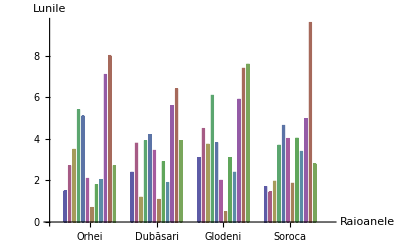

```mathematica
Needs["BarCharts`"]
BarChart[{{1.5,2.4,3.1,1.7},{2.7,3.8,4.5,1.45},{3.5,1.2,3.75,1.97},{5.4,3.91,6.1,3.7},{5.1,4.2,3.81,4.65},{2.1,3.45,2.01,4.02},{0.7,1.09,0.5,1.87},{1.8,2.9,3.1,4.04},{2.03,1.9,2.4,3.4},{7.1,5.6,5.91,4.97},{8.01,6.4,7.4,9.6},{2.7,3.9,7.6,2.8}},BarLabels->{"Orhei","Dubăsari","Glodeni","Soroca"},AxesLabel->{"Raioanele","Lunile"}]
```

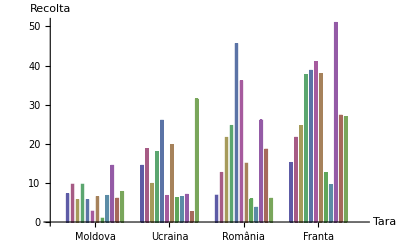

```mathematica
Needs["BarCharts`"]
BarChart[{{7.21,14.5,6.9,15.21},{9.7,18.69,12.67,21.67},{5.7,9.87,21.64,24.56},{9.7,17.94,24.68,37.6},{5.7,26.03,45.6,38.79},{2.81,6.78,36.07,41.02},{6.47,19.78,15.06,37.95},{1.02,6.23,5.91,12.6},{6.78,6.49,3.78,9.5},{14.5,7.08,26.08,51.02},{6.1,2.67,18.65,27.34},{7.8,31.45,6.08,26.91}},BarLabels->{"Moldova","Ucraina","România","Franta"},AxesLabel->{"Tara","Recolta"}]
```

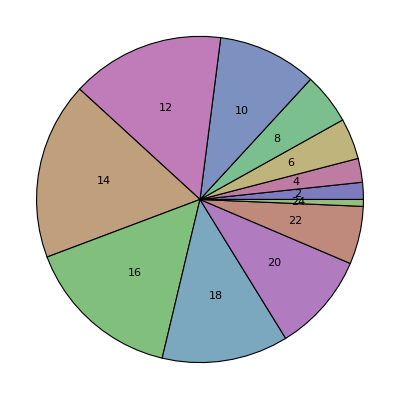

```mathematica
Needs["PieCharts`"]
PieChart[{0.5,0.7,1.2,1.5,2.9,4.5,5.2,4.6,3.7,2.9,1.7,0.2},PieLabels->{2,4,6,8,10,12,14,16,18,20,22,24}]
```

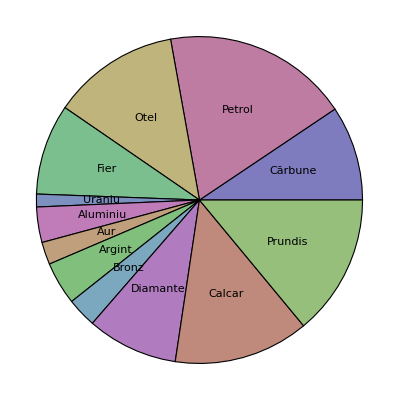

```mathematica
Needs["PieCharts`"]
PieChart[{12.6,24.75,16.91,12.05,1.7,4.7,2.98,5.71,3.94,12.11,17.98,18.75},PieLabels->{"Cărbune","Petrol","Otel","Fier","Uraniu","Aluminiu","Aur","Argint","Bronz","Diamante","Calcar","Prundis"}]
```

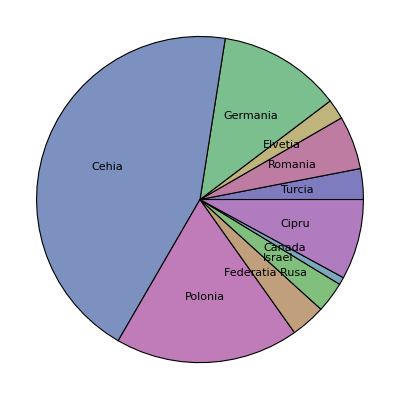

```mathematica
Needs["PieCharts`"]
PieChart[{2.3,4,1.5,9.2,33.3,13.7,2.6,2.3,1.4.40,6},PieLabels->{"Turcia","Romania","Elvetia","Germania","Cehia","Polonia","Federatia Rusa","Israel","Canada","Cipru","Spania"}]
```

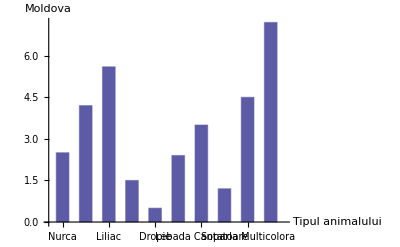

```mathematica
Needs["BarCharts`"]
BarChart[{{2.5,4.2,5.6,1.5,0.5,2.4,3.5,1.2,4.5,7.2}},BarSpacing->0.25,BarGroupSpacing->0.2 ,BarLabels->{"Nurca","Vidra","Liliac","Buhna","Dropie","Acvila","Lebada Cantatoare","Cocostarcul Negru","Soparla Multicolora","Pelican"},AxesLabel->{"Tipul animalului","Moldova"}]
```

```mathematica
{Limit[(x^2-8x+7)/(x^3-8 x^2+8x-1),x->1],Limit[Sin[8x+3 x^2]/ArcSin[2x-8 x^2],x->0],Limit[((8x+1)(8 x^2+3x-8))/(3x-8)^3,x->∞],Limit[(x^2-8x+1)/(x^2+8x+5),x->∞]}
```

{6/5,4,64/27,1}

```mathematica
{Limit[(√(x^2-6x+9))/(x-3),x->3],Limit[(x-5)/Abs[x-5],x->5],Limit[1/Tan[x],x->0],Limit[(x^2+8x)/(8 x^2+x+8),x->+∞]}
```

{1,1,∞,1/8}

```mathematica
{Limit[Limit[(x^2-8x*y+y^2+10)/(√x+x*y+8 y^2),x->1],y->2],Limit[Limit[x^2+2*x*y^8-3*x^8*y,x->1],y->-3],Limit[Limit[(x^2+y^2)/(8 x^2-y),x->∞],y->∞],Limit[Limit[Tan[8x*y+x^2*y^2]/ArcTan[x*y-8 x^2*y^2],x->0],y->0]}
```

{-1/35,13132,1/8,8}

```mathematica
{D[x^2+8x+Log[x]-Sinh[x],x],D[(8x-1)^5 Sin[8x],x],D[(8x+5)/(3x-8)+x^8 Log[2,x],x],D[x^(8xCos[x]),x]}
```

{8+1/x+2 x-Cosh[x],8 (-1+8 x)^5 Cos[8 x]+40 (-1+8 x)^4 Sin[8 x],8/(-8+3 x)-(3 (5+8 x))/(-8+3 x)^2+x^7/Log[2]+(8 x^7 Log[x])/Log[2],x^(8 xCos[x]) ((8 xCos[x])/x+8 Log[x] xCos'[x])}

```mathematica
D[(8x+1)(2x-8),{x,2}]
```

32

```mathematica
D[(8x+1)(2x-8),{x,3}]
```

0

```mathematica
D[(8x+1)/(3x+5),{x,2}]/.x->1
```

-111/256

```mathematica
D[(8x+1)/(3x+5),{x,3}]/.x->-2
```

1998

```mathematica
D[x^8/Log[ⅇ,x],{x,5}]/.x->ⅇ
```

3386 ⅇ^3

```mathematica
z=x^2+8xy+3 y^8-Sin[8xy]
```

x^2+8 xy+3 y^8-Sin[8 xy]

```mathematica
D[z,{x,2}]
```

2

```mathematica
D[z,{x,1},{y,1}]
```

0

```mathematica
D[z,{y,1},{x,1}]
```

0

```mathematica
D[z,{y,2}]
```

168 y^6

```mathematica
z=ArcTan[(8x)/y]
```

ArcTan[(8 x)/y]

```mathematica
D[z,{x,2}]
```

-(1024 x)/((1+(64 x^2)/y^2)^2 y^3)

```mathematica
D[z,{x,1},{y,1}]
```

(1024 x^2)/((1+(64 x^2)/y^2)^2 y^4)-8/((1+(64 x^2)/y^2) y^2)

```mathematica
D[z,{y,1},{x,1}]
```

(1024 x^2)/((1+(64 x^2)/y^2)^2 y^4)-8/((1+(64 x^2)/y^2) y^2)

```mathematica
D[z,{y,2}]
```

-(1024 x^3)/((1+(64 x^2)/y^2)^2 y^5)+(16 x)/((1+(64 x^2)/y^2) y^3)

```mathematica
y=3 x^5-5 x^3+8
(*DVA*)
Solve[Denominator[y]==0,x]
```

8-5 x^3+3 x^5

{}

```mathematica
(*Stabilim punctele critice y'=0*)
Solve[D[y,x]==0,x]
```

{{x→-1},{x→0},{x→0},{x→1}}

```mathematica
(*Determinam semnul derivatei pe intervalele*)
D[y,x]/.x->{-1,2,5}
```

{0,180,9000}

```mathematica
{Subscript[y, min]=y/.x->-1,Subscript[y, max]=y/.x->1}
```

{10,6}

```mathematica
y=x/(x^2+8^2)
(*DVA*)
Solve[Denominator[y]==0,x]
```

x/(64+x^2)

{{x→-8 ⅈ},{x→8 ⅈ}}

```mathematica
(*Stabilim punctele critice y'=0*)
Solve[D[y,x]==0,x]
```

{{x→-8},{x→8}}

```mathematica
(*Determinam semnul derivatei pe intervalele*)
D[y,x]/.x->{1,3,5}
```

{63/4225,55/5329,39/7921}

```mathematica
{Subscript[y, min]=y/.x->-8,Subscript[y, max]=y/.x->8}
```

{-1/16,1/16}

```mathematica
y=(8x)/Log[ⅇ,x]
(*DVA*)
Solve[Denominator[y]==0,x]
```

(8 x)/Log[x]

{{x→1}}

```mathematica
(*Stabilim punctele critice y'=0*)
Solve[D[y,x]==0,x]
```

{{x→ⅇ}}

```mathematica
(*Determinam semnul derivatei pe intervalele*)
D[y,x]/.x->{0,2,6}
```

{0,-8/Log[2]^2+8/Log[2],-8/Log[6]^2+8/Log[6]}

```mathematica
{Subscript[y, min]=y/.x->ⅇ,Subscript[y, max]=y/.x->ⅇ}
```

{8 ⅇ,8 ⅇ}